# Cold Plasma Roots nx(nz) with Plasma Profiles

## Open Additional files:

## Set Parameters by opening a Slab Parameter Window Get dispersion routines by evaluating Disper_no_package.nb Get plotting and printing routines by evaluating PlotPack.nb

## Plot Real and Imaginary parts of both roots nz from 4th order cold plasma dispersion relation

Define n-perp module and do plotting

```mathematica
nParallel2FS[x_]:=Module[{ne,b,x0},x0=x;ne=nprof[x0];b=bprof[x0];ColdDis2FS[freq,ne,b,nz,etaList]]
```

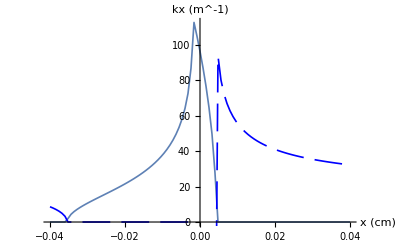

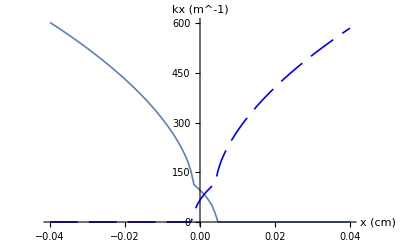

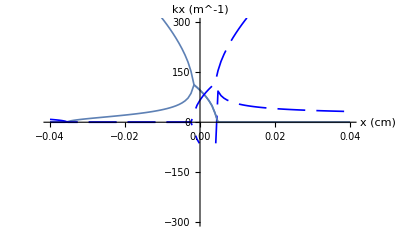

```mathematica
nt2FS=Table[Flatten[{x,k0 nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=ComplexListPlot[nF,"x (cm)","kx (m^-1)"]
g2=ComplexListPlot[nS,"x (cm)","kx (m^-1)"]
Show[{g1,g2},PlotRange->{-300,300}]
```

## Plot Real and Imaginary parts of both roots nz from 4th order cold plasma dispersion relation

Define n-perp module and do plotting

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;ne=nprof[x0];b=bprof[x0];ColdDis2FS[freq,ne,b,nz,etaList]]
```

```mathematica
nt2FS=Table[Flatten[{x,k0 nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=ComplexListPlot[nF,"x (cm)","kx (m^-1)"]
g2=ComplexListPlot[nS,"x (cm)","kx (m^-1)"]
Show[{g1,g2},PlotRange->{-300,300}]
```

-Graphics-

-Graphics-

-Graphics-

Plot S, R and L functions of cold plasma dispersion

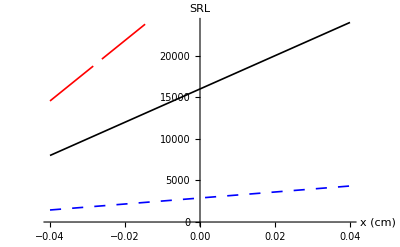

```mathematica
SRLplot[x_]:=Module[{ne,b,x0},x0=x;ne=nprof[x0];b=bprof[x0];SRL[freq,ne,b,nz,etaList]]
nt=Table[Flatten[{x,SRLplot[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
VectorListPlot[nt,"x (cm)","SRL"]
```

```mathematica
Show[%,PlotRange->{-500,500}]
```

⁃Graphics⁃

```mathematica
SRL[-.30]
```

{-269.4864350311406,251.528175260846,-790.5010453231273}

```mathematica
g1=VectorListPlot[nt,"x (cm)","SRL",DisplayFunction->Identity];
g2=Plot[N[NT/((rmaj+x) k0)]^2,{x,xmin,xmax},DisplayFunction->Identity];
Show[g1,g2]
paramPrint[{ne0,nsep,B,freq,NT,nz,etaList,TList,rmaj,rmin,rsep,sol,alphan}];
```

⁃Graphics⁃

20
ne0=1.2 10
           19
nsep=2.4 10
B=5
freq=40
NT=12
nz=13.773
etaList={1., 0, 0., 0., 0.}
TList={5., 5., 5., 5., 5., 5.}
rmaj=0.79
rmin=0.25
rsep=0.22
sol=0.02
alphan=0.35

```mathematica
Show[%445,%467,PlotRange->{-1000,1000}]
```

⁃Graphics⁃

## Initialization

```mathematica
Needs["`PlotPack`"]
```

$Failed

Magnetic field, Density and Temperature Profiles

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```